```mathematica
Clear["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks

```mathematica
$ProcessorCount
```

14

## Filter Scheme

P ϕ'=1/h Q (𝕀+σ R^-1 S)ϕ

### Interior

β Δ̂ f_(i-2)+α Δ̂ f_(i-1)+Δ̂ f_i+α Δ̂ f_(i+1)+β Δ̂ f_(i+2)=∑_(m=1)^(n/2) a_m(f_(i-m)-2 f_i+f_(i+m))
Use Taylor series to determine constraint equations for a_m

T(κ)=1+(2∑_(m=1)^(n/2) a_m[cos(m κ)-1])/(1+2α cos(κ) + 2β cos(2κ))

```mathematica
InteriorKimSpectral[order_,κ_,aList_]:=1+(2Sum[aList[[m]](Cos[m κ]-1),{m,1,order/2}])/(1+2α Cos[κ]+2β Cos[2κ])
```

```mathematica
KimFilterInterior[order_]:=Module[{aList,n,system,coeffs},
n=order/2;
aList=Table[Symbol["a"<>ToString[i]],{i,1,n}];
coeffs=Flatten[Append[aList,{α,β}]];
system={};
AppendTo[system,InteriorKimSpectral[order,κc,aList]==1/2];
Do[
AppendTo[system,Sum[j^i aList[[j]],{j,1,n}]==0]
,{i,2,order-1,2}];

AppendTo[system,InteriorKimSpectral[order,π,aList]==0];
AppendTo[system,(D[InteriorKimSpectral[order,κ,aList],{κ,2}]/.κ->π)==0];
system=system//Simplify;
(*Print[system];*)

Solve[system,coeffs]
]
interiorCoeffs=KimFilterInterior[6][[1]]//FullSimplify
```

{a1→-(30 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a2→(12 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a3→-(2 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),α→(4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),β→1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])}

### Boundary

#### Polynomial Generator

```mathematica
(*κc=0.7π;
ϵ=0.09*)

(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
(*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}]
numBoundaryRows=Length@RHSPars
fOrder=(2*Length@RHSPars)+1;
dhatfOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+dhatfOrder-1;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowdhatf1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowdhatf=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,dhatfOrder-1}];


matf=PrependTo[rowf,rowf1];
matdhatf=PrependTo[rowdhatf,rowdhatf1];
LMat=Join[matf,matdhatf];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["dhatf",ToString[i]]],{i,0,dhatfOrder-1}]];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]]//FullSimplify;

P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

(*other info to print?*)
Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Coefficients:\n",MatrixForm[pCoeffs]]
```

{a1,a2,a3}

3

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12) = (f0
f1
f2
f3
f4
f5
f6
dhatf0
dhatf1
dhatf2
dhatf3
dhatf4
dhatf5)

Coefficients:
(p0→f0
p1→dhatf0
p2→-(71 dhatf0)/15-30 dhatf1-75 dhatf2-(200 dhatf3)/3-(75 dhatf4)/4-(6 dhatf5)/5-(45647 f0)/3600-41 f1-(125 f2)/4+(400 f3)/9+(575 f4)/16+(113 f5)/25+f6/36
p3→(35009 dhatf0)/3600+112 dhatf1+(635 dhatf2)/2+(880 dhatf3)/3+(1345 dhatf4)/16+(136 dhatf5)/25+(138229 f0)/4000+(2746 f1)/15+(3625 f2)/24-(5080 f3)/27-(15355 f4)/96-(7666 f5)/375-(137 f6)/1080
p4→(-7434570 dhatf0-116472600 dhatf1-369751500 dhatf2-356748000 dhatf3-104537250 dhatf4-6856920 dhatf5-29576323 f0-212315220 f1-199423125 f2+218312000 f3+197148375 f4+25692948 f5+161345 f6)/648000
p5→(748530 dhatf0+14208600 dhatf1+49695600 dhatf2+50229600 dhatf3+15101850 dhatf4+1006680 dhatf5+3161977 f0+27863300 f1+30007550 f2-29068800 f3-28181225 f4-3758852 f5-23950 f6)/86400
p6→(-2286390 dhatf0-49483800 dhatf1-187751700 dhatf2-198952800 dhatf3-61556850 dhatf4-4181400 dhatf5-10019158 f0-102210180 f1-124870125 f2+107984000 f3+113466750 f4+15547908 f5+100805 f6)/518400
p7→(223080 dhatf0+5307750 dhatf1+21556500 dhatf2+23919000 dhatf3+7633500 dhatf4+529830 dhatf5+1001707 f0+11393225 f1+15542375 f2-12088000 f3-13875875 f4-1960457 f5-12975 f6)/144000
p8→(-325230 dhatf0-8307900 dhatf1-35716500 dhatf2-41394000 dhatf3-13646250 dhatf4-970380 dhatf5-1485722 f0-18364830 f1-27535125 f2+19366000 f3+24425250 f4+3570222 f5+24205 f6)/864000
p9→(5370 dhatf0+144900 dhatf1+653400 dhatf2+788400 dhatf3+268650 dhatf4+19620 dhatf5+24843 f0+327750 f1+532500 f2-340000 f3-472875 f4-71718 f5-500 f6)/86400
p10→(-3450 dhatf0-97200 dhatf1-456300 dhatf2-571200 dhatf3-201150 dhatf4-15120 dhatf5-16114 f0-223920 f1-389475 f2+226400 f3+347850 f4+54864 f5+395 f6)/518400
p11→(180 dhatf0+5250 dhatf1+25500 dhatf2+33000 dhatf3+12000 dhatf4+930 dhatf5+847 f0+12275 f1+22625 f2-12000 f3-20375 f4-3347 f5-25 f6)/432000
p12→(-30 dhatf0-900 dhatf1-4500 dhatf2-6000 dhatf3-2250 dhatf4-180 dhatf5-142 f0-2130 f1-4125 f2+2000 f3+3750 f4+642 f5+5 f6)/2592000)

#### Node 2

```mathematica
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]

scheme0=β dhatf0+α dhatf1+dhatf2+α dhatf3+β dhatf4-(a3 P[-1]+a2 f0+a1 f1-2(a1+a2+a3)f2+a1 f3+a2 f4+a3 f5);(*==0*)
schemedhatf5=Solve[β dhatf1+α dhatf2+dhatf3+α dhatf4+β dhatf5==+a3 f0+a2 f1+a1 f2-2(a1+a2+a3)f3+a1 f4+a2 f5+a3 f6,dhatf5][[1]];
scheme0=scheme0/.schemedhatf5//FullSimplify;
schemebd=γ20 dhatf0+γ21 dhatf1+γ22 dhatf2+γ23 dhatf3+γ24 dhatf4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)

fVars2={dhatf0,dhatf1,dhatf2,dhatf3,dhatf4,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd;(*==0*)
eq=Collect[eq,fVars2];

coeffEqs2={};
For[i=1,i<=Length[fVars2],i++,
AppendTo[coeffEqs2,Coefficient[eq,fVars2[[i]]]==0]]

bdCoeffs2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};


coeffEqs2;

bdCoeffs2=Solve[coeffEqs2,bdCoeffs2][[1]]/.interiorCoeffs;
coeffs2={γ22->(γ22/γ22/.bdCoeffs2),
γ20->(γ20/γ22/.bdCoeffs2),
γ21->(γ21/γ22/.bdCoeffs2),
γ23->(γ23/γ22/.bdCoeffs2),
γ24->(γ24/γ22/.bdCoeffs2),
a20->(a20/γ22/.bdCoeffs2),
a21->(a21/γ22/.bdCoeffs2),
a22->(a22/γ22/.bdCoeffs2),
a23->(a23/γ22/.bdCoeffs2),
a24->(a24/γ22/.bdCoeffs2),
a25->(a25/γ22/.bdCoeffs2),
a26->(a26/γ22/.bdCoeffs2)}
```

{γ22→1,γ20→((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (1/6-(84 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),γ21→((-(1176 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])+(4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),γ23→((84 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])+(4 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),γ24→((336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(1260 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])+(1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),a20→(-(840 Cos[κc/2]^8)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+(1628 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))/(5 (1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))),a21→((1008 Cos[κc/2]^8)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+(2322 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),a22→(-(2520 Cos[κc/2]^8)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+(2490 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),a23→((3360 Cos[κc/2]^8)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(2480 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),a24→(-(2520 Cos[κc/2]^8)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(2340 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])),a25→(6 Cos[κc/2]^4 ((840 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-263 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))),a26→(-(168 Cos[κc/2]^8)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(2 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))/(1/6+(336 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])-(4200 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))}

#### Node 1

```mathematica
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]

scheme0=β P'[-1]+α dhatf0+dhatf1+α dhatf2+β dhatf3-(a3 P[-2]+a2 P[-1]+a1 f0-2(a1+a2+a3)f1 +a1 f2+a2 f3+a3 f4); (*==0*)
schemedhatf5=Solve[β dhatf1+α dhatf2+dhatf3+α dhatf4+β dhatf5==+a3 f0+a2 f1+a1 f2-2(a1+a2+a3)f3+a1 f4+a2 f5+a3 f6,dhatf5][[1]];
schemedhatf4=Solve[γ20 dhatf0+γ21 dhatf1+γ22 dhatf2+γ23 dhatf3+γ24 dhatf4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,dhatf4][[1]];
scheme0=scheme0/.schemedhatf5;
scheme0=scheme0/.schemedhatf4/.coeffs2;
schemebd=γ10 dhatf0+γ11 dhatf1+γ12 dhatf2+γ13 dhatf3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)

fVars1={dhatf0,dhatf1,dhatf2,dhatf3,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars1];

coeffEqs1={};
For[i=1,i<=Length[fVars1],i++,
AppendTo[coeffEqs1,Coefficient[eq,fVars1[[i]]]==0]]

bdCoeffs1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};

coeffEqs1;

bdCoeffs1=Solve[coeffEqs1,bdCoeffs1][[1]]/.interiorCoeffs;

coeffs1={γ11->(γ11/γ11/.bdCoeffs1),
γ10->(γ10/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
γ12->(γ12/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
γ13->(γ13/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a10->(a10/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a11->(a11/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a12->(a12/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a13->(a13/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a14->(a14/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a15->(a15/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a16->(a16/γ11/.bdCoeffs1)}
```

#### Node 0

```mathematica
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

scheme0=β P'[-2]+α P'[-1]+dhatf0+α dhatf1+β dhatf2-(a3 P[-3]+a2 P[-2]+a1 P[-1]-2(a1+a2+a3)f0+a1 f1+a2 f2+a3 f3); (*==0*)
schemedhatf5=Solve[β dhatf1+α dhatf2+dhatf3+α dhatf4+β dhatf5==a3 f0+a2 f1+a1 f2-2(a1+a2+a3)f3+a1 f4+a2 f5+a3 f6,dhatf5][[1]];
schemedhatf4=Solve[γ20 dhatf0+γ21 dhatf1+γ22 dhatf2+γ23 dhatf3+γ24 dhatf4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,dhatf4][[1]];
schemedhatf3=Solve[γ10 dhatf0+γ11 dhatf1+γ12 dhatf2+γ13 dhatf3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6,dhatf3][[1]];
scheme0=scheme0/.schemedhatf5;
scheme0=scheme0/.schemedhatf4/.coeffs2;
scheme0=scheme0/.schemedhatf3/.coeffs1;
schemebd=γ00 dhatf0+γ01 dhatf1+γ02 dhatf2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)

fVars0={dhatf0,dhatf1,dhatf2,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars0];

coeffEqs0={};
For[i=1,i<=Length[fVars0],i++,
AppendTo[coeffEqs0,Coefficient[eq,fVars0[[i]]]==0]]

bdCoeffs0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};

coeffEqs0;

bdCoeffs0=Solve[coeffEqs0,bdCoeffs0][[1]]/.interiorCoeffs;

coeffs0={γ00->(γ00/γ00/.bdCoeffs0),
γ01->(γ01/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
γ02->(γ02/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a00->(a00/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a01->(a01/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a02->(a02/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a03->(a03/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a04->(a04/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a05->(a05/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a06->(a06/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*))}
```

#### Dump Saves

```mathematica
coeffs2 = coeffs2/.κc->(1-1ϵ)κc;
coeffs1 = coeffs1/.κc->(1-2ϵ)κc;
coeffs0 = coeffs0/.κc->(1-3ϵ)κc;

DumpSave["bdCoeffs2.mx","Global`coeffs2"]
DumpSave["bdCoeffs1.mx","Global`coeffs1"]
DumpSave["bdCoeffs0.mx","Global`coeffs0"]
```

{Global`coeffs2}

{Global`coeffs1}

{Global`coeffs0}

### Building the Matrix

#### Full Matrix

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),a00,
If[(i==k&&j==k-1),a01,
If[(i==k&&j==k-2),a02,
If[(i==k&&j==k-3),a03,
If[(i==k&&j==k-4),a04,
If[(i==k&&j==k-5),a05,
If[(i==k&&j==k-6),a06,
If[(i==k-1&&j==k),a10,
If[(i==k-1&&j==k-1),a11,
If[(i==k-1&&j==k-2),a12,
If[(i==k-1&&j==k-3),a13,
If[(i==k-1&&j==k-4),a14,
If[(i==k-1&&j==k-5),a15,
If[(i==k-1&&j==k-6),a16,
If[(i==k-2&&j==k),a20,
If[(i==k-2&&j==k-1),a21,
If[(i==k-2&&j==k-2),a22,
If[(i==k-2&&j==k-3),a23,
If[(i==k-2&&j==k-4),a24,
If[(i==k-2&&j==k-5),a25,
If[(i==k-2&&j==k-6),a26,


If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j, a0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];

LHS[10]//MatrixForm
RHS[10]//MatrixForm
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0
a2 | a1 | a0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
a3 | a2 | a1 | a0 | a1 | a2 | a3 | 0 | 0 | 0
0 | a3 | a2 | a1 | a0 | a1 | a2 | a3 | 0 | 0
0 | 0 | a3 | a2 | a1 | a0 | a1 | a2 | a3 | 0
0 | 0 | 0 | a3 | a2 | a1 | a0 | a1 | a2 | a3
0 | 0 | 0 | a26 | a25 | a24 | a23 | a22 | a21 | a20
0 | 0 | 0 | a16 | a15 | a14 | a13 | a12 | a11 | a10
0 | 0 | 0 | a06 | a05 | a04 | a03 | a02 | a01 | a00)

## Eigenvalue tests

### Kim 2007 Scheme

```mathematica
kimPent6th[n_]:=Module[{P,Q,α,β,a0,a1,a2,a3,γ01,γ02,γ10,γ12,γ13,γ20,γ21,γ23,γ24,γS12,γS13,γS20,γS21,γS23,γS24,b22Filter,b00,b01,b02,b03,b04,b05,b06,b10,b11,b12,b13,b14,b15,b16,b20,b21,b22,b23,b24,b25,b26,bS11,bS12,bS13,bS14,bS15,bS16,bS21,bS22,bS23,bS24,bS25,bS26},
α=0.5862704032801503;
β=0.09549533555017055;
a1=0.6431406736919156;
a2=0.2586011023495066;
a3=0.007140953479797375;

γ01=5.912678614078549;
γ02=3.775623951744012;
γ10=0.08360703307833438;
γ12=2.058102869495757;
γ13=0.9704052014790193;
γ20=0.03250008295108466;
γ21=0.3998040493524358;
γ23=0.7719261277615860;
γ24=0.1626635931256900;

b01=-3.456878182643609;
b02=5.839043358834730;
b03=1.015886726041007;
b04=-0.2246526470654333;
b05=0.08564940889936562;
b06=-0.01836710059356763;
b00=-(b01+b02+b03+b04+b05+b06);

b10=-0.3177447290722621;
b12=-0.02807631929593225;
b13=1.593461635747659;
b14=0.2533027046976367;
b15=-0.03619652460174756;
b16=0.004080281419108407;
b11=-(b10+b12+b13+b14+b15+b16);

b20=-0.1219006056449124;
b21=-0.6301651351188667;
b23=0.6521195063966084;
b24=0.3938843551210350;
b25=0.01904944407973912;
b26=-0.001027260523947668;
b22=-(b20+b21+b23+b24+b25+b26);

γS12=(γ12-γ10 γ02)/(1-γ10 γ01);
γS13=γ13/(1-γ10 γ01);
γS21=(γ10 γ21-γ20)/(γ10-γ20 γ12);
γS23=(γ10 γ23-γ20 γ13)/(γ10-γ20 γ12);
γS24=(γ10 γ24)/(γ10-γ20 γ12);

bS11=(b11-γ10 b01)/(1-γ10 γ01);
bS12=(b12-γ10 b02)/(1-γ10 γ01);
bS13=(b13-γ10 b03)/(1-γ10 γ01);
bS14=(b14-γ10 b04)/(1-γ10 γ01);
bS15=(b15-γ10 b05)/(1-γ10 γ01);
bS16=(b16-γ10 b06)/(1-γ10 γ01);

bS21=(γ10 b21-γ20 b11)/(γ10-γ20 γ12);
bS22=(γ10 b22-γ20 b12)/(γ10-γ20 γ12);
bS23=(γ10 b23-γ20 b13)/(γ10-γ20 γ12);
bS24=(γ10 b24-γ20 b14)/(γ10-γ20 γ12);
bS25=(γ10 b25-γ20 b15)/(γ10-γ20 γ12);
bS26=(γ10 b26-γ20 b16)/(γ10-γ20 γ12);

P=Table[0,{i,n},{j,n}];
P[[1,1]]=1;
P[[1,2]]=γS12;
P[[1,3]]=γS13;

P[[2,1]]=γS21;
P[[2,2]]=1;
P[[2,3]]=γS23;
P[[2,4]]=γS24;

P[[n,n]]=1;
P[[n,n-1]]=γ01;
P[[n,n-2]]=γ02;

P[[n-1,n]]=γ10;
P[[n-1,n-1]]=1;
P[[n-1,n-2]]=γ12;
P[[n-1,n-3]]=γ13;

P[[n-2,n]]=γ20;
P[[n-2,n-1]]=γ21;
P[[n-2,n-2]]=1;
P[[n-2,n-3]]=γ23;
P[[n-2,n-4]]=γ24;

Do[
P[[i,i]]=1;
If[(j==i-2)||(j==i+2), 
P[[i,j]]=β,
If[(j==i-1)||(j==i+1),
P[[i,j]]=α
]
]
,{i,3,n-3},{j,1,n}];

Q=Table[0,{i,n},{j,n}];
Q[[1,1]]=bS11;
Q[[1,2]]=bS12;
Q[[1,3]]=bS13;
Q[[1,4]]=bS14;
Q[[1,5]]=bS15;
Q[[1,6]]=bS16;

Q[[2,1]]=bS21;
Q[[2,2]]=bS22;
Q[[2,3]]=bS23;
Q[[2,4]]=bS24;
Q[[2,5]]=bS25;
Q[[2,6]]=bS26;

Q[[n,n]]=-b00;
Q[[n,n-1]]=-b01;
Q[[n,n-2]]=-b02;
Q[[n,n-3]]=-b03;
Q[[n,n-4]]=-b04;
Q[[n,n-5]]=-b05;
Q[[n,n-6]]=-b06;

Q[[n-1,n]]=-b10;
Q[[n-1,n-1]]=-b11;
Q[[n-1,n-2]]=-b12;
Q[[n-1,n-3]]=-b13;
Q[[n-1,n-4]]=-b14;
Q[[n-1,n-5]]=-b15;
Q[[n-1,n-6]]=-b16;

Q[[n-2,n]]=-b20;
Q[[n-2,n-1]]=-b21;
Q[[n-2,n-2]]=-b22;
Q[[n-2,n-3]]=-b23;
Q[[n-2,n-4]]=-b24;
Q[[n-2,n-5]]=-b25;
Q[[n-2,n-6]]=-b26;

Do[
If[(j==i-3), 
Q[[i,j]]=-a3,
If[(j==i+3),
Q[[i,j]]=a3,
If[(j==i-2), 
Q[[i,j]]=-a2,
If[(j==i+2),
Q[[i,j]]=a2,
If[(j==i-1), 
Q[[i,j]]=-a1,
If[(j==i+1),
Q[[i,j]]=a1
]
]
]
]
]
]
,{i,3,n-3},{j,1,n}];
Return[{Q,P}]
]
```

### Eigenvalue Calculation

```mathematica
κcList=Array[#&,600,{0.4999π,0.999π}];
ϵList={0}(*Array[#&,20,{0,1/3}]*);

k=160;

{Q,P}=kimPent6th[k];

Clear[xx,yy]
```

```mathematica
LaunchKernels[8]
```

{Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8)}

```mathematica
ParallelEvaluate[Directory[]]
```

{C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks}

```mathematica
ParallelEvaluate[Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs0.mx"]]
ParallelEvaluate[Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs1.mx"]]
ParallelEvaluate[Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs2.mx"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ParallelEvaluate[ValueQ[coeffs0]]
```

{True,True,True,True,True,True,True,True}

```mathematica
ParallelEvaluate[ByteCount[coeffs0]/2.^30]
```

{0.0426696,0.0426696,0.0426696,0.0426696,0.0426696,0.0426696,0.0426696,0.0426696}

```mathematica
DistributeDefinitions[interiorCoeffs,coeffs0, coeffs1,coeffs2,κcList, ϵList,LHS,RHS,LHSRows,RHSRows,k]
```

{interiorCoeffs,κcList,ϵList,LHS,LHSRows,RHS,RHSRows,k}

```mathematica
maxrelist=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy}];

γ22val=γ22/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ20val=γ20/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ21val=γ21/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ23val=γ23/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ24val=γ24/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a20val=a20/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a21val=a21/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a22val=a22/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a23val=a23/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a24val=a24/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a25val=a25/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a26val=a26/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
(* a26val=a26/.{coeffs2/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])}/.{yHat->yHat2List[[xx]]}; *)



γ11val=γ11/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ10val=γ10/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ12val=γ12/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ13val=γ13/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a10val=a10/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a11val=a11/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a12val=a12/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a13val=a13/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a14val=a14/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a15val=a15/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a16val=a16/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];



γ00val=γ00/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ01val=γ01/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ02val=γ02/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a00val=a00/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a01val=a01/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a02val=a02/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a03val=a03/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a04val=a04/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a05val=a05/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a06val=a06/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
(*γ00val=γ00val/γ00val/.{yHat->yHat0List[[zz]]};*)

αval = α/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
βval=β/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a1val=a1/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a2val=a2/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a3val=a3/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];

interior={α->αval,β->βval,a1->a1val,a2->a2val,a3->a3val};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];

(*Print[coeff];*)

LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[P].Q.(IdentityMatrix[k]+Inverse[LHSNum].RHSNum);
eigs=-Eigenvalues[mat];
{{κcList[[xx]],ϵList[[yy]]},Max[Re[eigs]]},
{xx,1,Length[κcList]},{yy,1,Length[ϵList]}];
```

```mathematica
maxrelist//TableForm;
Dimensions@maxrelist

trimmed=Flatten[maxrelist,1];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

{600,1,2}

{}

0

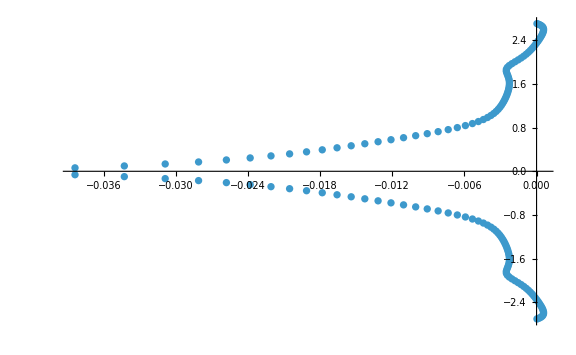

```mathematica
singleEigenvalueTest [κcVal_,ϵVal_,σ_]:= Module[{αval,βval,a0val,a1val,a2val,a3val,γ00val, γ01val,γ02val,γ10val,γ11val,γ12val,γ13val,γ20val,γ21val,γ22val, γ23val,γ24val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a20val,a21val,a22val,a23val,a24val,a25val,a26val, interior, boundary, coeff,LHSBars,RHSBars1,RHSBars2, barCoeffs, LHSNum, RHSNum, mat, eigs},
Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs0.mx"];
Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs1.mx"];
Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs2.mx"];

γ22val=γ22/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ20val=γ20/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ21val=γ21/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ23val=γ23/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ24val=γ24/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a20val=a20/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a21val=a21/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a22val=a22/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a23val=a23/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a24val=a24/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a25val=a25/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a26val=a26/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
(* a26val=a26/.{coeffs2/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])}/.{yHat->yHat2List[[xx]]}; *)



γ11val=γ11/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
γ10val=γ10/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
γ12val=γ12/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
γ13val=γ13/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a10val=a10/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a11val=a11/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a12val=a12/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a13val=a13/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a14val=a14/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a15val=a15/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a16val=a16/.coeffs1/.κc->κcVal/.ϵ->ϵVal;



γ00val=γ00/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
γ01val=γ01/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
γ02val=γ02/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a00val=a00/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a01val=a01/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a02val=a02/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a03val=a03/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a04val=a04/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a05val=a05/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a06val=a06/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
(*γ00val=γ00val/γ00val/.{yHat->yHat0List[[zz]]};*)

αval = α/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
βval=β/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a1val=a1/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a2val=a2/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a3val=a3/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a0val=-2(a1val+a2val+a3val);

interior={α->αval,β->βval,a0->a0val,a1->a1val,a2->a2val,a3->a3val};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];

(*Print[coeff];*)

LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[P].Q.(IdentityMatrix[k]+σ Inverse[LHSNum].RHSNum);
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},ImageSize->Large]
]

singleEigenvalueTest [0.85π,0,-0.002]
```